# AD_Excitation

## 1D ground state

## useful function

```mathematica
colors = { RGBColor[162/255,37/255,143/255],RGBColor[25/255,169/255,172/255],Orange};Load energy[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]][[-2]]
Load Time Step Energy gnorm[file_]:=ToExpression[StringReplace[StringSplit[ReadString[file]],"e"->"*10^"]]
```

## Heisenberg

#### relative error-χ

error exponentially-dependent on χ

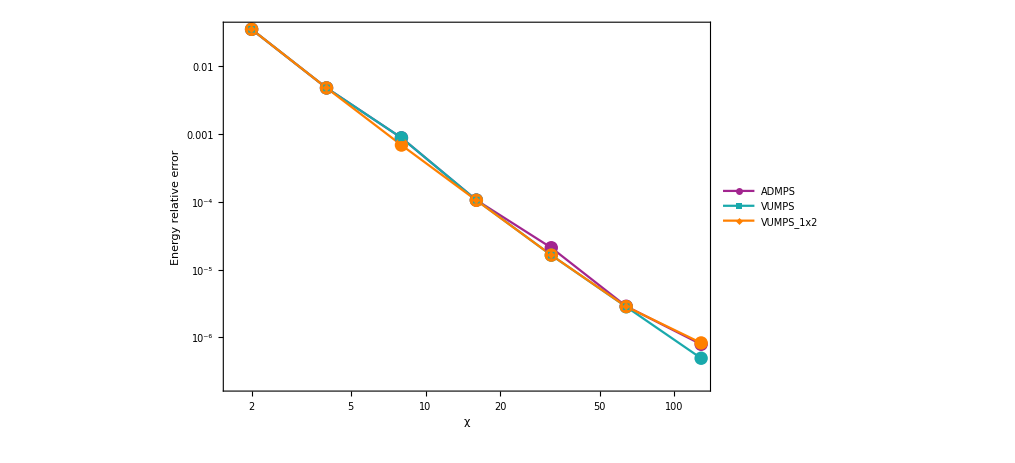

```mathematica
exact=0.25-Log[2];
AD MPS energy=Table[{2^i,Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1, 1.0, -1.0, -1.0)\\D2_χ"<>ToString[2^i]<>".log"]},{i,1,7}];
VUMPS energy={{2,-0.4279080104197335},{4,-0.44105819788743295},{8,-0.44276214977210915},{16,-0.4431005700103215},{32,-0.443139971582285},{64,-0.4431459279483812},{128,-0.4431469616755707}};
VUMPS12 energy={{2,-0.4279080104197335},{4,-0.44105819788743295},{8,-0.4428462940516308},{16,-0.4431009485966704},{32,-0.44313995986296106},{64,-0.44314592001143693},{128,-0.4431468127494822}};
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
VUMPS energy aberror=Table[{VUMPS energy[[i,1]],Abs[(exact-VUMPS energy[[i,2]])/exact]},{i,1,Length[VUMPS energy]}];
VUMPS12 energy aberror=Table[{VUMPS12 energy[[i,1]],Abs[(exact-VUMPS12 energy[[i,2]])/exact]},{i,1,Length[VUMPS12 energy]}];
ListLogLogPlot[{AD MPS energy aberror,VUMPS energy aberror,VUMPS12 energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotMarkers->Automatic,PlotLegends->Placed[{"ADMPS","VUMPS","VUMPS_1x2"},{Scaled[{0.7,0.5}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

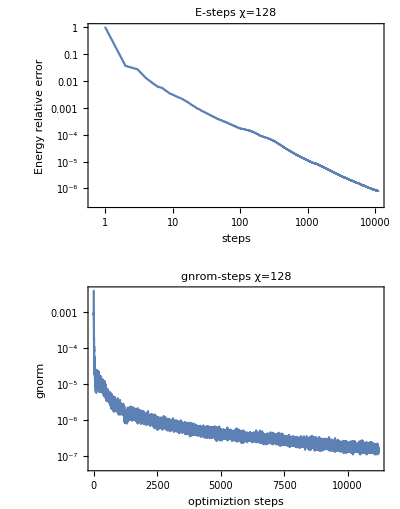

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Heisenberg{Float64}(0.5, 1.0, 1.0, 1.0)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## TFIsing at critical point g=1

#### relative error-χ

error exponentially-dependent on χ

Part::partd: 部分指定 colors⟦1⟧ 比对象深度更长.

Part::partd: 部分指定 colors⟦2⟧ 比对象深度更长.

Part::partd: 部分指定 colors⟦3⟧ 比对象深度更长.

General::stop: 在本次计算中，Part::partd 的进一步输出将被抑制.

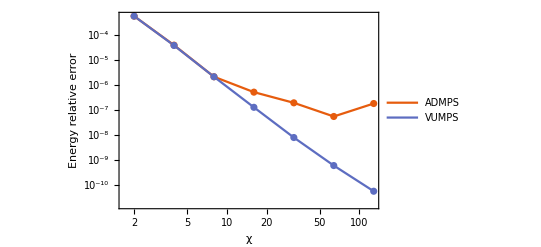

```mathematica
g=1;exact=Integrate[-1/(2Pi)Sqrt[g^2-2g Cos[k]+1],{k,0,2Pi}];
AD MPS energy={{2,-0.318135621484342},{4,-0.318297851395685},{8,-0.318309229736254},{16,-0.318309727151598},{32,-0.318309826702671},{64,-0.318309869258945},{128,-0.318309830392016}};
VUMPS energy={{2,-1.2725424859373686},{4,-1.2731927062998054},{8,-1.2732369270177255},{16,-1.273239387339872},{32,-1.2732395349825683},{64,-1.2732395439963544},{128,-1.2732395446657603}};
AD MPS energy=Table[{AD MPS energy[[i,1]],4 AD MPS energy[[i,2]]},{i,1,Length[AD MPS energy]}];
AD MPS energy aberror=Table[{AD MPS energy[[i,1]],Abs[(exact-AD MPS energy[[i,2]])/exact]},{i,1,Length[AD MPS energy]}];
VUMPS energy aberror=Table[{VUMPS energy[[i,1]],Abs[(exact-VUMPS energy[[i,2]])/exact]},{i,1,Length[VUMPS energy]}];
ListLogLogPlot[{AD MPS energy aberror,VUMPS energy aberror},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS","VUMPS"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"Energy relative error",None},{HoldForm["χ"],None}},ImageSize->400]
```

#### relative error-steps

error exponentially-dependent on steps

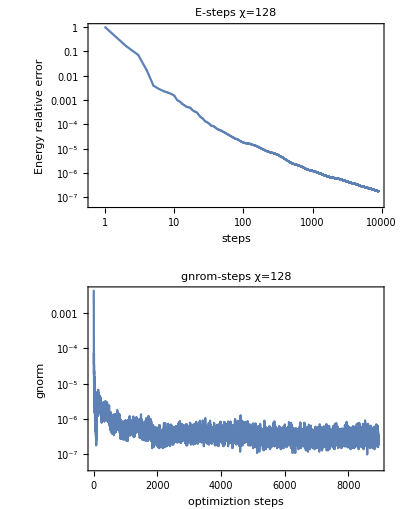

```mathematica
data=Load Time Step Energy gnorm["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\TFIsing{Float64}(0.5, 0.5)\\D2_χ128.log"];GraphicsGrid[{{ListLogLogPlot[Table[{i,Abs[(data[[4(i-1)+3]]-exact)/exact]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["Energy relative error"],None},{HoldForm["steps"],None}},PlotLabel->HoldForm["E-steps χ=128"],LabelStyle->{GrayLevel[0]},PlotRange->All]},{ListLogPlot[Table[{i,data[[4(i-1)+4]]},{i,1,Length[data]/4}],Joined->True,Mesh->All,PlotTheme->"Detailed",FrameLabel->{{HoldForm["gnorm"],None},{HoldForm["optimiztion steps"],None}},PlotRange->All,PlotLabel->HoldForm["gnrom-steps χ=128"]]}},ImageSize->400]
```

## 1D Excitation

## U1

```mathematica
U1 = {{0.44214127746903376-0.36649815518214574I,-0.13700868205515632-0.16528649180042596I},{0.1370086836991797+0.1652864904376679I, 0.23346510468812767-0.1935230536660265I}};
U2 = {{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}
```

{{Cos[x],-Sin[x]},{Sin[x],Cos[x]}}

```mathematica
FindRoot[Tr[Transpose[U1].U2]==0,{x,1}]
```

{x→1.5708+0.535137 ⅈ}

```mathematica
U=U2/.{x->1.5707963267948966+0.5351372028447591 ⅈ}
```

{{7.02112×10^-17-0.561047 ⅈ,-1.14664-3.43542×10^-17 ⅈ},{1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17-0.561047 ⅈ}}

```mathematica
FullSimplify[Transpose[U].U]
```

{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,1.+0. ⅈ}}

```mathematica
ConjugateTranspose[U]
```

{{7.02112×10^-17+0.561047 ⅈ,1.14664-3.43542×10^-17 ⅈ},{-1.14664+3.43542×10^-17 ⅈ,7.02112×10^-17+0.561047 ⅈ}}

## XXZ Δ=1

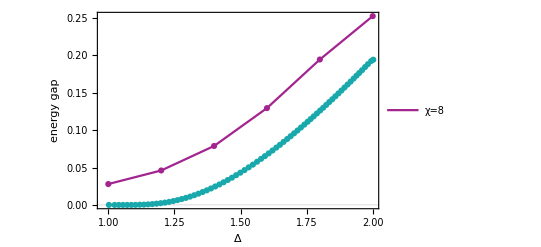

```mathematica
gap={0.05582453026702144,0.09212963838012368,0.15765165546585008,0.25902554676265305,0.38907021917034657,0.5051298373530196}/2;
energy gs=Table[{1.0+0.2(i-1),Load energy["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\XXZ{Float64}("<>ToString[NumberForm[1.0+0.2(i-1),{2,1}]]<>")\\D2_χ8.log"]},{i,1,6}];
energy gap=Table[{energy gs[[i,1]],gap[[i]]},{i,1,Length[gap]}];
Exact = Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\project\\XXZ_gap.csv"];
ListPlot[{energy gap,Exact },PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8"},{Scaled[{0.7,0.8}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"Δ",None}},ImageSize->400]
```

## Heisenberg S=1/2

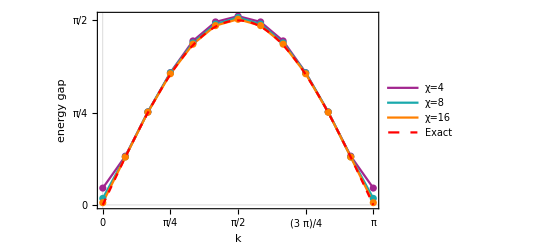

```mathematica
gap={{0.143590951236512,0.41530630963142906,0.7919144836295847,1.1263906176088896,1.3962166412387695,1.5578014262286415,1.6073219940962598,1.5578014252762273,1.3962166412329813,1.1263906186752397,0.791914483411365,0.415306313325118,0.14359095621658013},{0.055825535280367065,0.40920812813787655,0.7917343968681471,1.124766271557226,1.379519702559978,1.5398361831063736,1.5948824096077312,1.5398361216280303,1.3795198076975546,1.1247663680286026,0.791734354199969,0.40920812220705727,0.055826048730513896},
{0.019355656610179933,0.40749600807271985,0.7893265909061853,1.116831940068277,1.368569477493216,1.526614821143771,1.5805417601476666,1.5266152002333788,1.3685691333818455,1.116831994201616,0.7893267774108071,0.40749554338175925,0.01936395160433102}};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,3},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=4","χ=8","χ=16"},{Scaled[{0.7,0.2}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi},PlotLegends->Placed[{"Exact"},{Scaled[{0.6,0.8}], {0, 0}}],PlotStyle->{Dashed,Red},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]}]]
```

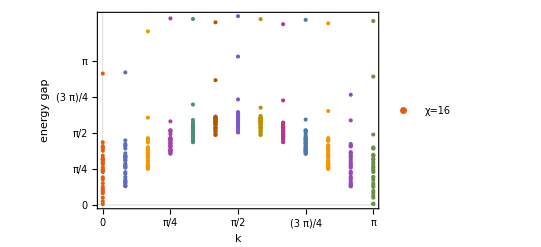

```mathematica
data={{0.019356712019114892,0.07988399537000476,0.15851980030219873,0.25463892314106706,0.287120756397108,0.30459423982442213,0.3479629943878291,0.3922590290112449,0.4730370929326074,0.5577705457747633,0.6004789242641874,0.718590070430259,0.7439289900867999,0.7495836084115252,0.7821209734141411,0.8229444507585456,0.8971681651337648,0.901995097855716,0.9439744124606408,0.9696428965384598,0.9958241788054643,1.0041003694226043,1.0054805948271819,1.0745533155732234,1.180929290460144,1.2325044004821992,1.2532894962360224,1.2837474621301057,1.3667881667284276,2.8646066019201752,},{0.40749545997731024,0.4142511021698713,0.43356413933476184,0.475406537485462,0.49283245623109206,0.5028117913747882,0.5287702964271762,0.5571428958544163,0.6106206879634741,0.6803569308483806,0.714178426296922,0.8115120209843482,0.8356798773101553,0.8374586977078984,0.8699178607399839,0.9019830647090546,0.9712917165007591,0.9737498932970463,1.0115021472245342,1.0364849155901132,1.055766434877827,1.0687115459542742,1.068754854037054,1.1253272036295503,1.2306250163019161,1.2817346376112082,1.3021807343637686,1.3300632810400672,1.4075640707087964,2.8889855941756273,},{0.7893266944597348,0.7942501629158961,0.8080983901196898,0.8329832624770432,0.8371042143663318,0.8485798469746656,0.8607240204576377,0.8770320060315122,0.8965651986306411,0.9528899687030133,0.97344525072165,1.0335063173750503,1.0485824510180348,1.0591232417233063,1.085525173213311,1.0985179256179807,1.1558025583204596,1.1603245206639765,1.1890467276198426,1.210974787432773,1.2127473679440022,1.2341645845777038,1.238221476027026,1.2593986762292515,1.3637136820530713,1.4147349287917201,1.4351944870496096,1.455853661606546,1.9035620925279053,3.7848677083057747,},{1.116831502605037,1.12476530849907,1.15430460646794,1.1687978477015146,1.1799055417539226,1.193694864650017,1.2010668235112858,1.201140538762355,1.2091965592227063,1.2590291983596569,1.2695786907497852,1.2892016469960854,1.293902273245662,1.3274472663598187,1.3388464110793226,1.351369027978242,1.3802791573229731,1.3931407515569652,1.4233732296129213,1.4258267355362826,1.4319920587187818,1.4419554188371382,1.4510467492380943,1.4647142285637693,1.5417525377787744,1.5971300132545627,1.620147193335427,1.6285552425540075,1.8219652516480467,4.066599204359205,},{1.3685689761889452,1.376751307097338,1.417512024110783,1.4435360358612712,1.4655676725300586,1.4894342455817675,1.4964296394145618,1.4989335515925373,1.5005635828143817,1.529068157428938,1.540174901301829,1.5487475185851236,1.549745216104134,1.568148444458624,1.5951481865176167,1.6000923532044522,1.6027327280920682,1.6164856580165312,1.6169190387860428,1.6699323819821772,1.6731677946889956,1.678444718734378,1.6849843360854513,1.7034394313919503,1.7217408643561687,1.763768502785001,1.7960796086984125,1.8504555137484338,2.190241957087645,4.055459789874986,},{1.5266146074808955,1.5351495579404821,1.5852007179262673,1.6093648946563477,1.636486546352942,1.6681632428651025,1.6823737812163686,1.6844391306143944,1.6847106624278922,1.7385630207524074,1.759565796077722,1.762173773125544,1.7701121016717183,1.7983222443292795,1.8105773125905387,1.8126719689438504,1.8155815421714279,1.8327868545942116,1.8381796981024656,1.8615650039854224,1.8678147252962165,1.8779402568886399,1.8924265833368583,1.8939565537326823,1.8943462671356877,1.905613231280845,1.9090383533701487,1.9254452214636193,2.72055401273043,3.9819833812412218,},{1.5805411732081112,1.5886593033410528,1.641749100020726,1.665547988944231,1.6991894622430865,1.7327092534729733,1.743381215790137,1.7497299643816298,1.7512167174567566,1.7918517854271931,1.8197636782730775,1.8212953766296298,1.825514991333764,1.8725561523658738,1.8909546742403205,1.8951320551583912,1.9045335366632057,1.9117764622737465,1.920216706315951,1.9711582067056597,1.9810155992977627,1.9947806931276375,1.9962842709797617,1.9965842909499656,2.0106626043637825,2.010819084407383,2.02378002915089,2.3005953636131786,3.235245494623999,4.116815393592645,},{1.5266146138295849,1.5337556104531076,1.585200740724084,1.6038439808725744,1.6364865104873207,1.6681635510681518,1.6823743144080967,1.6844387184175804,1.6929936377195653,1.730416462551267,1.7597857149708078,1.762173721632632,1.7701122211897062,1.7983223863939903,1.8105776141303231,1.8126718024052313,1.821274003365932,1.8327869465416147,1.8381795434754769,1.8440545833225725,1.8668261790832716,1.8779400494286325,1.8800024063408864,1.8924270460964727,1.8939575179101493,1.9056128515933148,1.9090378879259335,1.93987840005778,2.120094532159012,4.051593416680396,},{1.3685689764707742,1.3740018027016563,1.4175120848230747,1.4341878776695516,1.4655678198986097,1.489434552371823,1.4964299453534982,1.5005633268494591,1.5065077555628699,1.5135155761110382,1.5401749811009575,1.5483409819989356,1.548747165873286,1.5681498852450781,1.5951490487159559,1.6027322561778543,1.6156936862333289,1.6164862103488604,1.61691878927919,1.6633651250986146,1.6699333721222533,1.6784439961118993,1.703438341852252,1.7106140402687966,1.7136607038689378,1.7637669518331391,1.779810296957471,1.7960831218801239,2.278523198771948,3.9406181549128902,},{1.1168315115650753,1.1207256917563961,1.1543046308875105,1.160738320405532,1.1799055623809236,1.1936950195808922,1.2011408221233486,1.2091967975413735,1.2153399744747992,1.2466981314308494,1.2574855989210585,1.269577526050929,1.2892022380823884,1.327449384795426,1.3388470200992217,1.351368767498939,1.3721818850663645,1.3931413016927126,1.42337462783548,1.4258258587337995,1.4319929567168939,1.4646458055137497,1.4647136636986695,1.5074935543002541,1.5528414394724142,1.5971359155909663,1.6201469299457782,1.6285599198032636,1.8610595953487552,4.035370165640145,},{0.7893266963883178,0.7913374803738014,0.80809848355993,0.8154143044684896,0.8329832684142604,0.8485804862629531,0.8770323231891377,0.8917846288044309,0.8965655139162783,0.9466469949855978,0.9719074984729527,0.9734429173911155,1.0335067709653576,1.059123422951192,1.0855250948258277,1.0985209435743524,1.1220578572457651,1.160324874589181,1.1890460611067981,1.212751030826172,1.2382221841192163,1.2593986095342762,1.2739426924891868,1.3025837838412864,1.3957009117589567,1.4147438170082063,1.4351942444313903,1.4558556418346649,2.0483544183513422,3.9593347538821706,},{0.40749546536827774,0.40832868355849616,0.4335642927414416,0.44972609512798917,0.4754064545027773,0.5028128058092911,0.5571433015687848,0.5838917988115573,0.6106208674872218,0.6707863030727833,0.7141743390620788,0.7228397998790248,0.8115122447729578,0.8356807001116999,0.8699179445069521,0.9019865286637174,0.9212591100229373,0.9712921208859898,1.0115017943993811,1.055770828421495,1.0687574401044815,1.1253270284754826,1.1283875952837439,1.1503946181792346,1.2768589231067016,1.2817457004444024,1.3021805897405276,1.3300656037606284,1.8439581798161688,2.402502242249594,},{0.019356809950179597,0.029916300562974875,0.1585200675923619,0.1981441049937934,0.2546389233505662,0.30459575025163155,0.39225940990771535,0.43130061036785206,0.47303709405531175,0.5453999132929324,0.6004734606841438,0.6122869967014534,0.7185900761089724,0.7439301071199007,0.7821209792088036,0.8229479832735931,0.8412597973315288,0.8971684032726289,0.9439744118898505,0.9958274004267408,1.0041054365803053,1.0732846893904768,1.0745533266265916,1.0933159940135706,1.2323046279511454,1.2325162441319775,1.253289496260357,1.5347002921036776,2.7990200297345713,4.010786579441088,}};
energy gap=Table[Transpose@{Table[Pi/12 (i-1),{j,1,Length[data[[i]]]}],data[[i]]},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=16"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

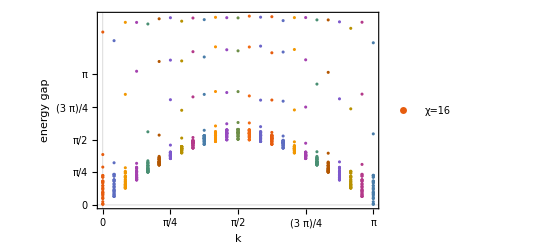

```mathematica
data={{0.018758895893593808,0.018758896234207345,0.0283048615354895,0.07800391466670797,0.15635173907396438,0.15635173918392575,0.1906284609366582,0.2432776555248377,0.24327765566186166,0.28245944966877046,0.29326287994913414,0.29326288002062184,0.3283390933118122,0.38450002963134444,0.3845000296574652,0.4160208869435229,0.4654702847764459,0.46547028491622067,0.5326092414275717,0.5340605380700828,0.5676252037744685,0.567625203834877,0.5790385821413772,0.6688515901368273,0.668851590240734,0.7081194369997363,0.708119481128795,0.9113333075164485,1.2132650688214675,4.161841524631899,},{0.2053914207844365,0.205391420791889,0.20650387086637578,0.21779965440026205,0.2540619174137635,0.2540619174512093,0.2761595649775448,0.3138384588010541,0.31383845885483175,0.3446050261624337,0.3537355497269298,0.3537355497323259,0.38283235554025974,0.43142275793423124,0.4314227579602049,0.4592722805361352,0.5032266287898829,0.5032266289159477,0.5666418076462474,0.5673688501491856,0.5993425148957503,0.5993425149291215,0.6094041012287468,0.694666540495711,0.6946665405828008,0.7327551120940382,0.7327570294976556,0.7387569025255245,1.0149745855950076,3.9543850393584803,},{0.4073879320560634,0.4073879320613052,0.4080695175334198,0.413414001615549,0.43226347551999666,0.4322634755532683,0.44520272838673847,0.4693349001788937,0.46933490022393964,0.4879481841194534,0.4952058048297385,0.495205804840403,0.5151312040864464,0.5505765697596492,0.5505765697789815,0.5714547976076745,0.603930839183311,0.6039308393133828,0.6579991519630694,0.6587698361912809,0.6859026017905194,0.6859026018291456,0.6935798233990952,0.7671810379182279,0.7671810380099994,0.8023746186682581,0.8043025171522427,0.894865300090504,2.661892334326733,4.395381022263707,},{0.6034026175094581,0.6034026175104292,0.6043588254692082,0.6076663766636163,0.6206344551610465,0.6206344551808183,0.6292312998201017,0.6481732772593233,0.6481732772931109,0.6580185747182697,0.6659637314081754,0.6659637314193101,0.6793365874285053,0.7051911020522964,0.705191102074887,0.7203635688052198,0.7404242034403538,0.7404242035665725,0.7857430105450688,0.7882180491456934,0.8094817892630601,0.8094817892946408,0.8137181157256499,0.8738886829162337,0.8738886830069761,0.9022207767557168,0.9062015265254447,1.0013784011091709,3.2180478996193367,4.393707489981292,},{0.7892471509241338,0.7892471509257244,0.7911591649071444,0.794106897621783,0.8074346117837842,0.8074346117974465,0.8131079798147725,0.8304047180505889,0.8304047180774224,0.8328118491836554,0.8440169199243034,0.8440169199331788,0.8532239727173013,0.8724582385004482,0.8724582385111659,0.8835015728975286,0.8911716162240626,0.8911716163298382,0.9313776527848017,0.9368510131929795,0.9529293677890258,0.9530364036925988,0.9530364037216829,1.0004084101472879,1.0004084102287718,1.0192588146168033,1.0318590355365145,1.0627669278653196,1.7602082890393342,4.356091228973746,},{0.9611707180884304,0.9611707180975146,0.9640710968960368,0.9679724059848624,0.9876997042582405,0.9876997042641886,0.9918860715848833,1.0041557545741153,1.0090731751993016,1.0090731752272144,1.0209568347360136,1.0209568347461206,1.0279010230934618,1.0410373903348593,1.0410373903603787,1.0451865890976844,1.0451865891667755,1.0490895888210998,1.081317803479126,1.092979713771563,1.1012650851196641,1.104809918567684,1.1048099185988756,1.1348600438538752,1.1348600439305407,1.1445612806398675,1.1685019992389691,1.6809900098775423,3.453164173932563,4.480901166001464,},{1.1167458917483852,1.1167458917504858,1.1202802225151707,1.1247126853984628,1.1539520983356453,1.1539520983573242,1.159869035578997,1.1675212484162536,1.1792858548560172,1.1792858548804783,1.1915896523291007,1.1915896523440732,1.197291344379043,1.197291344447491,1.1979434197640209,1.207172445443838,1.2071724454482253,1.2104419254245724,1.2290829976385613,1.249467280980073,1.2523575061429284,1.257427137247439,1.2574271372854013,1.2693721474237138,1.2698632613483196,1.272214649589968,1.4404320206348336,2.5328920201898586,3.486187908756946,4.506761374780178,},{1.2533711830951855,1.2533711830985645,1.2575142811170203,1.2616791279498405,1.2968684960728631,1.2968684961062955,1.3081349475253716,1.315936756297699,1.3339967313402712,1.333996731366729,1.3494503319658835,1.3494503319894153,1.3521777686745378,1.3521777686961678,1.3570354457670175,1.362592764220243,1.362592764228453,1.3639683934801574,1.3739703743708085,1.3922805938098448,1.401773415357157,1.4017734153892667,1.4029588412418648,1.4058225748428277,1.4058227202015445,1.4075353376671143,1.6098935332425937,2.2786273466634235,3.466433839753329,4.423586737162433,},{1.3684587258260401,1.368458725832221,1.3733808168730661,1.3769816453024564,1.416566815007618,1.41656681503471,1.4303444677150055,1.4407507446950398,1.4621389737794415,1.462138973805141,1.4854727779961898,1.4854727780006576,1.4930751887731148,1.4947185360613608,1.4947185360917168,1.5001977885243072,1.5001977885366629,1.5050740075608167,1.509560197176088,1.524045698180808,1.5353956118082568,1.5353956118290364,1.5450601388613088,1.5462573494806917,1.5475172203895313,1.5576427374396038,1.623385939072185,2.6008480898774993,3.689091385162307,4.499776713998229,},{1.4599729452520933,1.4599729452651322,1.46568022080142,1.4687811799484618,1.5136988201476114,1.5136988201770245,1.5267796969817877,1.539249147307551,1.5610179538017994,1.561017953842062,1.587762518568955,1.5877625185799418,1.5970893615374964,1.60395138817618,1.6039513882594372,1.607221342309852,1.6072213423321295,1.6164062024633663,1.6310908806729838,1.639786359014234,1.6628302987313202,1.662830298770612,1.6662572548169097,1.66688987812602,1.6670912704562815,1.6693589819920227,1.796970259278937,2.6609733488497063,3.5616632512134316,4.4604911706439285,},{1.5264713051581749,1.526471305166025,1.53263703303161,1.535624607526344,1.584692255025713,1.5846922550502303,1.5984081914977524,1.61008784573685,1.6339824443376954,1.6339824443757185,1.662310117857294,1.662310117866113,1.6733523632175185,1.6765992296262733,1.6765992297236658,1.681538832511498,1.6815388325245262,1.692425132752871,1.7119961291689523,1.7287738857903117,1.7493222439633553,1.753509900116189,1.7535099015083813,1.753791666704834,1.7595088438185869,1.759516531364976,1.9012379016148155,2.730236259455667,3.805674302700666,4.516468999878706,},{1.5668775473940761,1.5668775473973404,1.573085224834058,1.5764204201067773,1.6266868376010217,1.626686837643346,1.6446219004345586,1.6502691809627716,1.6800664938094625,1.680066493855617,1.7102501171047668,1.7102501171075433,1.7227208033074763,1.7257148655812204,1.7257148656369272,1.7287652489469052,1.7287652489910301,1.7379287224846625,1.7625724741605306,1.7717962009859947,1.7983023507685343,1.8007218768648117,1.8007460995030362,1.8038822129313232,1.8059411349690846,1.8059411512298915,1.9537015083391511,2.7058434255906496,3.7353209240892413,4.507710448666527,},{1.580440264331192,1.5804402643446678,1.5865866588835977,1.5901784567674133,1.6403576767243042,1.6403576767616663,1.661254035302549,1.6626991119747154,1.6960342805903355,1.6960342806398416,1.727232280864548,1.7272322808823333,1.7403830004817897,1.74276950811714,1.7427695081482413,1.7481835903964935,1.7481835904495737,1.7530426002338584,1.7716457062520816,1.7962561655407168,1.815422762240292,1.815422766460228,1.8156508347449678,1.8160027334163011,1.818014781679449,1.8180148537950243,1.9839697927670026,2.728400087741231,3.7093590826271563,4.502775632983955,},{1.5668775473889114,1.5668775473975927,1.5730852248350853,1.576420420109788,1.626686837603953,1.6266868376478207,1.644621900442536,1.6502691809646388,1.6800664938245733,1.6800664938670982,1.710250117106746,1.7102501171116995,1.7227208033234982,1.7257148655845833,1.7257148656385803,1.7287652489505594,1.7287652489944667,1.7379287224937991,1.7625724741625803,1.7717962009910506,1.798302350778114,1.8007218768687088,1.8007460995087556,1.800761634770877,1.8059411349610597,1.805941135746934,1.9739632636653104,2.624291887494193,3.802295685794788,4.545189305565087,},{1.5264713051588918,1.5264713051630254,1.5326370330262844,1.5356246075312476,1.584692255027981,1.5846922550570197,1.5984081914962815,1.6100878457375343,1.633982444340686,1.633982444381861,1.6623101178560005,1.6623101178655542,1.6733523632267975,1.6765992296340704,1.6765992297415713,1.6815388325246432,1.6815388325358587,1.6924251327523645,1.7119961291886094,1.7287738857938786,1.7493222439720795,1.7535099001385166,1.7535101063974428,1.7537916667187752,1.7595088438260584,1.7595893272912404,1.8841305349420767,2.523080696679755,3.8230844744693293,4.5197711748885085,},{1.459972945259058,1.4599729452628063,1.4656802208001902,1.4687811799463726,1.5136988201436403,1.5136988201661457,1.5267796969833385,1.539249147300106,1.5610179538087576,1.5610179538308806,1.5877625185650488,1.587762518569415,1.597089361532307,1.6039513881771135,1.6039513882458847,1.607221342306968,1.607221342324198,1.6164062024518129,1.6310908806717013,1.6397863590152975,1.6628302987354284,1.6628302987620305,1.6662572548094614,1.6670912704432128,1.6693589819841075,1.6851152524656685,1.7459039764540367,2.5255845777533485,3.662547602853922,4.531221748288603,},{1.3684587258294956,1.3684587258318668,1.3733808168684765,1.3769816453008459,1.416566815009502,1.4165668150377804,1.4303444677092716,1.4407507446974048,1.4621389737793677,1.462138973804136,1.4854727779964698,1.4854727780019312,1.4930751887720166,1.4947185360603619,1.4947185360917457,1.50019778852619,1.500197788538948,1.5050740075591271,1.5095601971763044,1.5240456981783104,1.535395611811287,1.535395611832137,1.5450601388531031,1.546257349475904,1.5475172203875585,1.5576427666607529,1.6586812977951735,2.498049419353778,3.6809796750338535,4.4370109295079745,},{1.253371183097137,1.2533711831011736,1.2575142811247477,1.261679127949045,1.2968684960765444,1.2968684961083072,1.3081349475250166,1.3159367562984021,1.3339967313502379,1.3339967313691397,1.3494503319756446,1.3494503319932734,1.3521777686858898,1.3521777687017578,1.357035445769212,1.3625927642230733,1.3625927642282796,1.3639683934846523,1.3739703743797624,1.3922805938198788,1.4017734153624033,1.401773415394486,1.4029588412531158,1.4058225748385558,1.4075353376783362,1.4318217092168144,1.5188097326061194,2.2867809167529822,3.741667747735052,4.509390936557237,},{1.1167458917464845,1.1167458917510742,1.1202802225179567,1.1247126854023872,1.1539520983484757,1.1539520983629235,1.1598690355805916,1.1675212484189057,1.1792858548667273,1.1792858548813259,1.191589652334779,1.1915896523479945,1.197291344383298,1.1972913444483195,1.1979434197673988,1.2071724454445567,1.2071724454501287,1.2104419254214962,1.2290829976404143,1.2494672809777192,1.2523575061398518,1.25742713725617,1.2574271372776635,1.2693721474038957,1.269409114155463,1.2722146495855828,1.4856518240933871,2.356289497039544,3.493315967095686,4.510706505198625,},{0.9611707180915937,0.961170718096203,0.9640710968947958,0.9679724059836949,0.9876997042600753,0.9876997042646112,0.9918860715857567,1.004155754573148,1.0090731752003141,1.0090731752182225,1.020956834737262,1.0209568347445868,1.0279010231006378,1.04103739033211,1.0410373903526282,1.0451865891026486,1.0451865891635408,1.0490895888208331,1.0813178034777857,1.0929797137737673,1.1012650851142791,1.104809918566113,1.1048099185909874,1.1348600438509562,1.1348600439238234,1.1445612806428986,1.168501999195788,1.2802883516784345,2.9092242570412523,4.454434548000633,},{0.789247150921811,0.7892471509309602,0.7911591649062305,0.7941068976159823,0.807434611785109,0.8074346117949366,0.8131079798140366,0.8304047180531384,0.8304047180745069,0.832811849186443,0.8440169199217216,0.8440169199291107,0.8532239727161111,0.8724582384959764,0.8724582385087837,0.8835015728943336,0.8911716162158352,0.8911716163301941,0.9313776527851916,0.9368510131878802,0.952929367786099,0.9530364036899006,0.9530364037195057,1.0004084101495208,1.0004084102336044,1.0192010789831607,1.0318590703839456,1.2456661426169,3.1916923167511966,4.453816202977481,},{0.6034026175014656,0.6034026175116883,0.6043588254620336,0.6076663766626418,0.6206344551588021,0.6206344551703402,0.6292312998147336,0.6481732772592097,0.648173277284922,0.6580185747116906,0.6659637313976366,0.6659637314128403,0.6793365874239576,0.7051911020394432,0.7051911020591979,0.7203635687981156,0.7404242034264541,0.7404242035478573,0.7857430105307343,0.7882180491222848,0.8094817892532478,0.8094817892839812,0.8137181157131131,0.873888682920279,0.8738886829995203,0.9022207767429538,0.9062015359746054,1.036462153898585,2.5543209315305124,4.407521039326538,},{0.40738793206718305,0.40738793207037916,0.4080695175376672,0.41341400161924136,0.4322634755209044,0.4322634755482586,0.4452027283881278,0.46933490018351154,0.46933490022170155,0.48794818412157237,0.49520580483729393,0.49520580484403787,0.5151312040935346,0.5505765697583871,0.5505765697882189,0.5714547976110074,0.6039308391831301,0.6039308393239786,0.6579991519630828,0.6587698361929196,0.6859026017969497,0.6859026018331036,0.6935798234043022,0.7671810379212612,0.7671810380201225,0.8023746186956228,0.8043393203639678,0.8119601939567462,2.313463487839275,4.251530460951028,},{0.2053914207751104,0.20539142082023032,0.20650387075412646,0.21779965437671422,0.2540619174006278,0.25406191742560114,0.2761595649773334,0.3138384588148515,0.3138384588553087,0.3446050261540663,0.35373554971311916,0.35373554971925936,0.38283235553532136,0.43142275792765783,0.4314227579690386,0.45927228053073077,0.5032266287904408,0.5032266289173245,0.5666418076428035,0.5673688501533345,0.5993425148991165,0.5993425149290509,0.6094041012323088,0.6946665404947973,0.6946665405814151,0.7327551121293279,0.7384604967415884,0.9757359707897476,2.6675947815521033,4.398351248175913,},{0.01875889581504775,0.018758895874744885,0.028304861528990033,0.07800391461951817,0.15635173907336997,0.15635173912009814,0.19062846094195462,0.24327765553231062,0.24327765556731684,0.28245944965882397,0.29326287995277456,0.2932628799592465,0.3283390932821765,0.3845000296075939,0.3845000296432891,0.4160208869146177,0.46547028478395414,0.465470284914111,0.5326092414135452,0.5340605380587691,0.5676252037667165,0.5676252037983074,0.5790385821522918,0.6688515901584199,0.6688515902395913,0.7081194369611783,0.7081194655321641,0.7152455080851206,1.7107078774906608,3.9036158457964683,}};
energy gap=Table[Transpose@{Table[Pi/24 (i-1),{j,1,Length[data[[i]]]}],data[[i]]},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=16"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

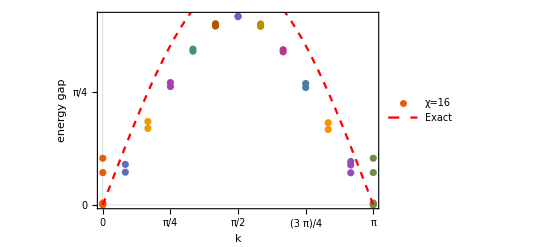

```mathematica
data={{-5.112435149516763,-5.106389323608165,-5.099060398033465,-4.887172014435088,-4.787240642731671,},{-4.884394637682965,-4.82989522272906,},{-4.579411301101019,-4.531686939721455,},{-4.288129033974117,-4.260437816504813,},{-4.041637161167749,-4.027451946152251,},{-3.86672028473775,-3.8611556458985525,-3.8507013795127327,},{-3.801211807277366,-3.797538642576671,},{-3.8686895483638395,-3.86272290349122,-3.8518189527475624,},{-4.046130632365421,-4.03123143850453,},{-4.294729398596706,-4.267130487136753,},{-4.586710861248851,-4.539802393852298,},{-4.888558319687279,-4.834179433912235,-4.8100238438555944,},{-5.112435149512656,-5.106389323616154,-5.099060398043641,-4.887172014437653,-4.7872406427300325,}};
energy gap=Table[Transpose@{Table[Pi/12 (i-1),{j,1,Length[data[[i]]]}],data[[i]]+5.112435149516763},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=16"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi},PlotLegends->Placed[{"Exact"},{Scaled[{0.6,0.8}], {0, 0}}],PlotStyle->{Dashed,Red},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]}]]
```

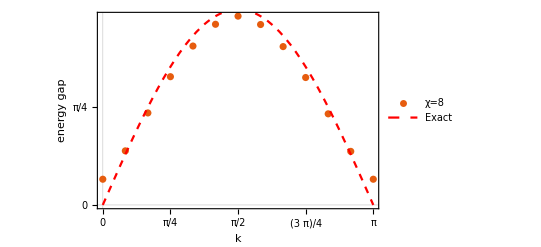

```mathematica
data={0.20668151959234837,0.43471795899496435,0.7396988534136808,1.030979624328884,1.277470672116598,1.4523875221726192,1.5178955157126168,1.4504159117567235,1.272974826127789,1.0243775726021553,0.7323984422712444,0.4305535753811993,0.20668151958306868};
gap=Table[{Pi/12 (i-1),data[[i]]},{i,1,Length[data]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=8"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi},PlotLegends->Placed[{"Exact"},{Scaled[{0.6,0.8}], {0, 0}}],PlotStyle->{Dashed,Red},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]}]]
```

#### merge two A

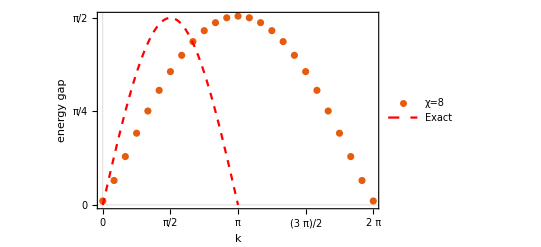

```mathematica
data={0.033199782966633506,0.20522931038147774,0.40628958402975723,0.6026077926287233,0.7890881949693977,0.9627672037677757,1.1198450149595573,1.2568752293209928,1.3719763340079838,1.463829859971666,1.531038105720195,1.572171932577538,1.5860451576164545,1.572171933049515,1.531038106264603,1.4638298604805076,1.3719763344663312,1.2568752297302388,1.1198450153242967,0.9627672040908828,0.78908819526642,0.6026077929266308,0.40628958432607964,0.2052293107012697,0.03319978296635351};
gap=Table[{2Pi/24(i-1),data[[i]]},{i,1,Length[data]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=8"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi,5Pi/4,3Pi/2,7Pi/4,2Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],Plot[Pi/2Sin[x],{x,0,Pi},PlotLegends->Placed[{"Exact"},{Scaled[{0.6,0.8}], {0, 0}}],PlotStyle->{Dashed,Red},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]}]]
```

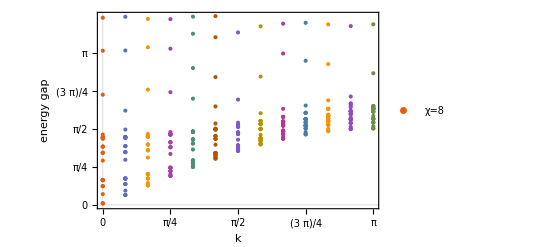

```mathematica
data={{0.03319978296663306,0.03319978438546789,0.03321067571277947,0.2234573302400964,0.3887344210526017,0.38873443371004357,0.38874888533493235,0.5141762144401202,0.5141762145255384,0.514223141825912,0.5142231613336098,0.5142387938419295,0.9188788671994293,1.0806695146172454,1.0806695397492119,1.0806982235839162,1.2082649206041265,1.2082649446231142,1.2082811289819508,1.3769244597417514,1.3769244804032625,1.3769384679162846,1.4001849957216737,1.400233434306423,1.4002425418069664,1.4002617048742734,1.4559790418276046,2.2839487616951932,3.1941517053228674,3.877908870594155,},{0.20522931038147774,0.2052293173578994,0.20523068896645835,0.2960449240140721,0.4332918855363235,0.43329189464626805,0.4333047863361905,0.5479952699559981,0.5479952736121863,0.5480391352491132,0.5480391527438874,0.5480537649752124,0.935192060456288,1.0941126009495237,1.0941126259945588,1.094140754314519,1.2184094786923072,1.2184095027100832,1.218425428414684,1.3863847850638735,1.3863848045939027,1.3863986218937088,1.4080610880181903,1.4081169533011724,1.40811793247948,1.4081368885866656,1.5617487433053385,1.9537311985474237,3.1994139360881872,3.8977410983154415,},{0.4062895840297568,0.40628958770044576,0.406290388076302,0.45478917936001206,0.5493182006882814,0.5493182061824512,0.5493280371818148,0.6402640308739578,0.6402640374960096,0.640300714158652,0.6403007271538889,0.64031294715352,0.9827099732946026,1.1336719058912792,1.1336719293053987,1.1336984666693672,1.2492375325079008,1.249237556106523,1.24925269209887,1.4133596251589382,1.4133596435621465,1.413373188278705,1.4310398658691474,1.4310865268023196,1.4310947167935961,1.4311130083381545,1.4717450911781178,2.388684195363834,3.2662052569627567,3.8535676870159263,},{0.6026077926287233,0.6026077960019156,0.6026085934220277,0.6336779004640097,0.7006410677926246,0.7006410723489773,0.7006481025672744,0.7707079376032488,0.7707079462389822,0.7707369600234759,0.7707369687062693,0.7707466369252454,1.0562511458064825,1.1960317445426976,1.1960317653806993,1.196056003232781,1.2977294357251776,1.297729458233548,1.2977434246721187,1.456472761740728,1.4564727788862193,1.4564859041057472,1.4672128009570846,1.467214523511289,1.4672644843762401,1.4672817178446491,1.5096493545986096,2.3348541316267006,3.236861111134456,3.848213237934444,},{0.7890881949693989,0.7890881977779199,0.7890895551155723,0.8121719624804061,0.8628871963653025,0.8628872005747887,0.8628920225602049,0.9202068087983633,0.9202068184829135,0.9202297940188994,0.9202298001451094,0.9202374571545462,1.147626154305513,1.2764841542454686,1.2764841721033449,1.2765057975015504,1.3595164447697734,1.3595164656410674,1.3595289761260527,1.5135180928489338,1.5135307176129145,1.5135692388437154,1.5135695413915298,1.5136171653556325,1.5136329764878937,1.5289944087005407,2.2020667280541737,2.835690683685831,3.545548504146894,3.899903680755174,},{0.962767203767776,0.9627672067770177,0.9627693794887412,0.9837127713873768,1.0252150754043605,1.0252150782701235,1.0252181069987267,1.0761066393367529,1.0761066493679377,1.0761255288640723,1.076125534059545,1.0761318263911144,1.2482612964506716,1.3697363808079168,1.3697363957769737,1.3697554671331935,1.429461697667766,1.4294617163814083,1.4294726078404267,1.5663496198484956,1.5663496352006845,1.5663924381654435,1.566392458643034,1.566406718164882,1.5817434940484962,1.6864590307171228,2.039729624423302,2.6484649416985935,3.47338541391545,3.911061134438394,},{1.1198450149595576,1.1198450188089042,1.1198480129759927,1.1438739591674287,1.1832156958919957,1.1832156970172334,1.1832174522589884,1.2311718059779433,1.2311718160050173,1.2311881859971252,1.231188190981145,1.231193647030871,1.3510748148914067,1.4705338356484254,1.4705338483666341,1.470550626115972,1.5024199306371009,1.5024199466170576,1.5024292457942188,1.6216265926161177,1.6216266052723465,1.6216643630441971,1.6216643789337228,1.6216769592033637,1.6581380060469568,1.6581380182879943,1.6581491487623772,1.7033435484681747,2.18260192194509,3.5729876944389174,},{1.2568752293209926,1.256875233497619,1.2568787374491643,1.288522953067482,1.3335767412483415,1.3335767415515176,1.3335780468796,1.38098321983947,1.3809832297936726,1.3809983744740446,1.3809983794624237,1.3810034270933782,1.4514462666098105,1.5711781928608541,1.5711782044809088,1.5711873739424842,1.5770739248678485,1.5770739269099794,1.5770874621740512,1.6760529114778087,1.6760529219131093,1.676085649170276,1.6760856615575632,1.6760965661537026,1.7397769679444142,1.7397769782400447,1.7397872574521935,1.8995332482835952,2.6592704082773637,3.6991327109058183,},{1.3719763340079838,1.3719763377095893,1.3719801273233263,1.412617826392418,1.4710785731065579,1.4710785739931975,1.4710802279634385,1.5216345670038924,1.521634576873489,1.521649810904658,1.521649816035459,1.5216548932931564,1.5479360663994235,1.6414136806995197,1.6414136907496628,1.6414187598618568,1.6776798968795177,1.6776799052767077,1.6776946757907338,1.727836833743229,1.7278368415984908,1.7278646312858752,1.7278646403050864,1.727873900144722,1.8239201882524954,1.823920196557207,1.8239295948117458,1.9912160415591291,3.1372577469317626,3.754751874746651,},{1.463829859971666,1.4638298628088613,1.463833931466435,1.5099680440302936,1.5856920698794896,1.5856920713928024,1.5856947484127035,1.6417092763847598,1.6459906471001753,1.6459906560986617,1.646008018765284,1.6460080240430877,1.6460138103671138,1.7104030494970055,1.7104030555326848,1.710406055448412,1.775733430667802,1.7757334396854656,1.775747816502695,1.7796471135672796,1.7796471179708648,1.7796694746685175,1.779669480403067,1.7796769301216346,1.9081221483115196,1.9081221639937072,1.9081307167435924,2.0596448967355503,2.9865060992225576,3.7726995732675377,},{1.531038105720195,1.5310381076649016,1.5310425132978134,1.5772699581656113,1.6612008845563664,1.661200886426339,1.6612043110503945,1.7313520419137363,1.734142249188302,1.7341422540012363,1.7341638359290972,1.7341638405865023,1.7341710325451163,1.791865856179303,1.7918658584494083,1.7918674254477336,1.8474434537328452,1.847443455967653,1.8474599780754568,1.8474599815924382,1.8474654873751153,1.8656602276165943,1.865660237490126,1.8656748272419317,1.989898638134167,1.98990651116116,1.9906947782882238,2.165672178943927,2.917126636308992,3.738920314655783,},{1.5721719325775378,1.5721719337906488,1.5721766527657044,1.616180133432787,1.6981319534571921,1.6981319548882565,1.6981351269464984,1.773886984387135,1.7738869860143944,1.7739096584140426,1.773909662099327,1.7739172173412385,1.8075963221127989,1.8796409914952348,1.8796409945969879,1.8796426905831576,1.9380639818453334,1.9380639889842737,1.9380797880503482,1.9380797931419558,1.9380850582192424,1.9410959712781244,1.9410959814293176,1.9411113628819276,2.0232180287135137,2.0635501495418365,2.0933617569704235,2.1050459650678617,2.24590194651164,3.704550853192031,},{1.586045157616455,1.5860451582731998,1.5860500103337005,1.6289112701206143,1.7090741829097096,1.7090741835555106,1.7090771382629528,1.7845903994678782,1.7845904005491988,1.7846128937349668,1.7846128969757316,1.784620392558664,1.8438714864178718,1.9320151211227794,1.9320151240764523,1.9320175953739311,1.978140838343295,1.978140847074085,1.9781571237325764,1.9976571986854066,2.001206152272914,2.0012061528960094,2.0012246990177003,2.001224704295026,2.0012308835853245,2.0470055009264705,2.0470055033087156,2.047006331390097,2.72820464859994,3.742445452063335,}};
energy gap=Table[Transpose@{Table[Pi/12 (i-1),{j,1,Length[data[[i]]]}],data[[i]]},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,PlotStyle->{},Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=8"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

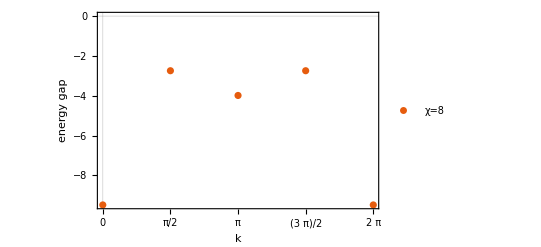

```mathematica
data={-9.484904614707462,-2.7429141723847668,-3.9854860276840203,-2.742914176112847,-9.484904614701337};
gap=Table[{Pi/2(i-1),data[[i]]},{i,1,Length[data]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->All,Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=8"},{Scaled[{0.5,0.2}], {0, 0}}],FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi,5Pi/4,3Pi/2,7Pi/4,2Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

## Heisenberg S=1

### energy gap err

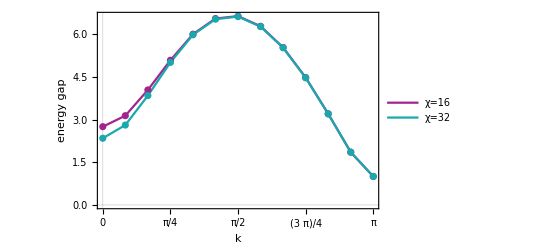

```mathematica
gap={{1.1268454257095815,1.285171785206961,1.6557565989884577,2.083020577151731,2.4584581883654395,2.6837600174326828,2.7185068607572935,2.572623823406021,2.2671755708120296,1.834096103535215,1.312574461976365,0.7600515284855315,0.4097919500865274}/0.4097919500865274,{0.9617463024620846,1.1519833989373156,1.5768092742171103,2.055853638229605,2.4543603583220612,2.67903976595536,2.7163927633731575,2.571772799105956,2.2668161567529386,1.834129470152294,1.3128049237356012,0.7604951249254354,0.4104726336238398}/0.4104726336238398};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,2},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=16","χ=32"},{Scaled[{0.7,0.2}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

### k = π energy gap error

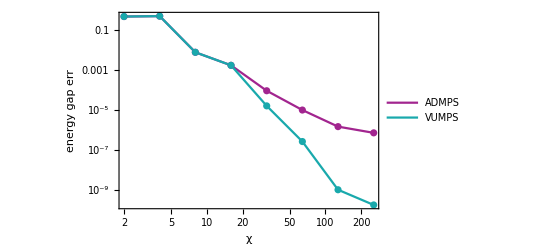

```mathematica
ADMPS={0.22222222138633316,0.2132164213483138,0.4073983283744025,0.4097915343423936,0.41044228122259074,0.410475228123841,0.41047865160632757,0.4104789568932946};
VUMPS={0.22222221626766125,0.2132164087305432,0.4073983291336687,0.4097915314728411,0.41047276288854273,0.4104791409770996,0.41047924804361297,0.4104792485361133};
Verstraete2012=0.410479248463;
ADMPS err=Table[{2^i,Abs[(ADMPS[[i]]-Verstraete2012)/Verstraete2012]},{i,1,Length[ADMPS]}];
VUMPS err=Table[{2^i,Abs[(VUMPS[[i]]-Verstraete2012)/Verstraete2012]},{i,1,Length[VUMPS]}];
Show[ListLogLogPlot[{ADMPS err,VUMPS err},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"ADMPS","VUMPS"},{Scaled[{0.6,0.5}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Table[2^i,{i,1,10}],Automatic}},FrameLabel->{{"energy gap err",None},{"χ",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400],PlotRange->All]
```

### excitation spectrum

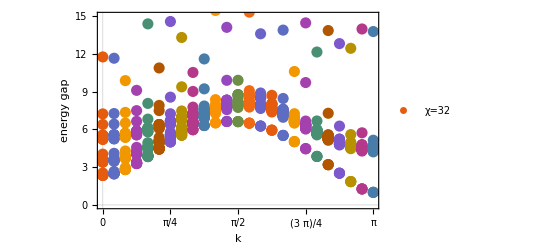

```mathematica
data={{0.9617463024619146,0.9634111720504643,0.9647352116045146,0.9800214077991101,0.9801990816546777,0.981882923125935,0.9824557903732202,0.983087168152062,1.0414864111968625,1.3931628722753235,1.398768371018499,1.40255699723393,1.4551705333279366,1.4555974429854461,1.4619227172139695,1.4643338133161279,1.466372328824409,1.6562115027948932,2.1356189921804964,2.1442160505785504,2.148077170666456,2.258543403052716,2.2591949991815543,2.26833879398281,2.2725432811247352,2.2747945436066317,2.623711551143167,2.9683187720426627,4.826674987461724,11.385963903151568,},{1.0129893524616018,1.0145778316487788,1.0158418212771387,1.0307018409684607,1.0308516312206295,1.032458067468372,1.032999437432671,1.0336018466125014,1.088826516482119,1.425954545923639,1.4314418629518197,1.4351375847045795,1.487000138976805,1.4872731313407432,1.493528979307147,1.4958913036453962,1.4978677329697154,1.6828478421753363,2.1529551920146943,2.161454106564456,2.165245672234796,2.27493075152407,2.2754256484551494,2.2845766457840537,2.2887594098128514,2.2909481772525284,2.6356945661691746,2.9802828952373814,4.783878292155997,11.554077754270518,},{1.1519833987599115,1.1533855220857243,1.1545110568494605,1.1690174198974905,1.1691565394806562,1.1705474942132437,1.1710183022055898,1.1715525515158551,1.2190596189551777,1.5189977425030432,1.5241525197378198,1.5276473325672548,1.5778435540372449,1.577978818825504,1.5838906568521258,1.586110378997359,1.5879518532917438,1.759549912022609,2.203404700747413,2.2115950436078453,2.21524602689231,2.3226369348807556,2.3230189775705106,2.331990910331933,2.3360821145846393,2.338195886074873,2.670781710060928,3.017939161777515,4.053717585320009,11.17507460704742,},{1.3487218993860755,1.3498945705126872,1.3508428014444722,1.3668489531262842,1.3669952766381754,1.3681281244387953,1.368519865582703,1.3689741850238257,1.4070208405441993,1.6591091414259838,1.663817311375894,1.6670548222276678,1.7163147757782813,1.7164053079554167,1.7217627068851296,1.723782935441969,1.7254448532285829,1.8778896184758684,2.2827009392357356,2.290414811490244,2.2938701825310703,2.3980593291145453,2.3984122131669983,2.407026022247699,2.410965362726323,2.412996354712241,2.72638161441483,3.074822212538379,3.7365090895965314,11.68449077590579,},{1.5768092743342914,1.577723175464949,1.5784677755658167,1.5994894419470984,1.5996517001541728,1.6005387629496084,1.6008582199315342,1.6012301882071975,1.6292719535667488,1.8307718006200555,1.8350096559437974,1.8379829370537906,1.8885654979771147,1.8887154916656017,1.8934030923994807,1.8952027621687448,1.8966652126128345,2.0268060126154523,2.3846397337019436,2.391767057808512,2.3949950327624143,2.495842315914869,2.4962442705712293,2.5043633493839708,2.508106273271114,2.5100496926329745,2.7987003298837902,3.3108173753531536,5.9049097402639354,11.389986909067547,},{1.8175617713348866,1.818170918218821,1.8186782011707814,1.8504122176750382,1.8505907662933483,1.8512602930176327,1.8515186068484035,1.8517993461985793,1.8692499900722563,2.0205919075152554,2.0243880167710198,2.0271243589472263,2.0818089587772337,2.0820131409462457,2.086033515168016,2.0876115388337007,2.0888674620964878,2.1951400610916845,2.5021826061208934,2.508672467474162,2.5116669375800176,2.609651585052504,2.6101345937275924,2.6176880262444437,2.6212072825718074,2.623060894842504,3.077011087074376,3.24488036518012,4.466673461210375,10.79875565671987,},{2.0558536382276755,2.0561229497047555,2.0563597364186963,2.1091499030213607,2.109341776808416,2.1098182863725636,2.110028773073764,2.110147851207202,2.1160716206130212,2.220166350691352,2.223548120897592,2.2260766355897026,2.285568230582489,2.285801323684514,2.2891931735858146,2.290554460060854,2.291596672656338,2.3731119965738925,2.6285549518204965,2.63440578841679,2.637184176657679,2.7329202798060845,2.7334852598002293,2.7404533611024102,2.743736179242064,2.7454993283350193,2.9731009917156985,3.5146866432851014,5.9812167626426405,11.490867185486087,},{2.2741098842858944,2.2741487143136316,2.2741835672853368,2.361300179860948,2.368671015554589,2.3688766819303946,2.36916371230791,2.3693147406991715,2.3696317484716163,2.4287673889747663,2.4316325055267507,2.433871185034608,2.491604020739309,2.491839296523352,2.4946415759635134,2.4957881448410717,2.4965958487280626,2.5529180369692748,2.758155925588651,2.7633988357725294,2.7659968588742005,2.859526398340002,2.8601611563756566,2.866551281250463,2.869592720960336,2.8712630447811813,3.063881263996921,3.851255821468586,5.460635352770831,11.197178769233746,},{2.454360358320965,2.4543840404735744,2.454395030258512,2.5985413869439347,2.622964656771726,2.623182709723295,2.623305560061313,2.6234282575426633,2.6235909063341483,2.6485053172530058,2.650667715736702,2.652417003312541,2.6932667954622467,2.6934753085180905,2.6957098794533754,2.696633524845122,2.6971527193583054,2.729482016091748,2.887078735226598,2.8917611959323937,2.8942291414586805,2.9846190409470337,2.985299945817023,2.9911160724643233,2.993905177407854,2.9954685533227225,3.188687633109149,3.701082620715657,4.320536649074297,12.036851668851591,},{2.58975206920159,2.5897836945213797,2.5898071913142107,2.8144196782648474,2.8634304943610798,2.863729244975937,2.8637546250405426,2.863911338870702,2.8639908935704663,2.871138535046818,2.8725731242248496,2.8737506661704284,2.8850987025210157,2.8852400781671164,2.8868939056273595,2.8875497345597743,2.887783561473166,2.9041223304287453,3.0127696956365564,3.016967862175588,3.0193931707252575,3.1069577263476256,3.1076268425411206,3.1127758957890928,3.115246496430252,3.1166343608886,3.226015981213981,3.7856773890646163,4.7611144726409975,11.89892190429484,},{2.6790397664905163,2.679057498189947,2.6790719550527466,2.9852204517340564,3.0552603232312885,3.0556485407183414,3.0561934149611654,3.056564527169519,3.056864344347792,3.0730558713732106,3.073231515687007,3.0741437849517106,3.074617272238279,3.0749048670742196,3.0807907646542843,3.081532892410048,3.081971342755789,3.0853332677400833,3.1337633995905096,3.1376659472097357,3.140303783660448,3.239537347370985,3.2400056268019846,3.243817447849093,3.2458497234350463,3.2464340583535742,3.4332837529813074,6.343201164758343,9.956660173053086,12.487350309046247,},{2.7212264691954267,2.7212351344163435,2.721240541895329,3.107129330648347,3.1954184969348436,3.195486994960258,3.196155501732453,3.196466565911473,3.196634978789054,3.2073378096264964,3.207516297442466,3.2091263436586748,3.2098516567409585,3.2104048129027136,3.22733890875448,3.2293697338000285,3.230340966304528,3.2391662727792836,3.269602250492992,3.2713418978283806,3.272791328649416,3.3748998380177477,3.4137580787460986,3.4140309594699425,3.4159619555255762,3.4170564876024603,4.063990340076408,5.791419859118088,10.178859253227996,12.481250977852618,},{2.7163927640300356,2.7163982562098195,2.716400609046903,3.1792455890604328,3.2620223674473094,3.2621612582477986,3.263577629746487,3.2642739848325517,3.2646449674031914,3.2966879230413046,3.296943916138059,3.2975096893164437,3.2980110494264165,3.298247451189833,3.307267189936181,3.309584614657509,3.3110434006416347,3.313142496323868,3.350888084568942,3.352653088498484,3.3532346741348933,3.494759236201832,3.58754115618471,3.5880129760966475,3.5932685005890126,3.5999911354530068,4.0647425312426755,7.12065523362396,10.126634180255692,12.41999381580641,},{2.6658098634748755,2.6658137561204716,2.6658155837351125,3.1909044032138816,3.271144952449515,3.2713972581104502,3.2721393220684445,3.2725609150673507,3.272803563181808,3.313285698169254,3.313657913722574,3.315068175673226,3.3159305965996326,3.3163834931622613,3.3249902534002125,3.326457928576305,3.326990694387331,3.327642616454851,3.349863577933225,3.3522636113223894,3.353727970203133,3.492833592024105,3.577215206474903,3.579121147525189,3.5798502650343664,3.6021734882817005,3.7256288297046516,6.287611723634415,9.436306987454087,12.74020811045537,},{2.571772799105757,2.5717752883029252,2.571776671176908,3.145719550279105,3.2164707347852697,3.216508208704296,3.2173629874437712,3.217795807153604,3.217974994995742,3.2511376077453824,3.2526967376858935,3.252803212501699,3.253888141911217,3.2546444394492027,3.2550167134442978,3.2642246219313518,3.2658355313467067,3.2666586803940922,3.274437653589965,3.2763155506812427,3.277150491538916,3.4798196642453756,3.4939705961066645,3.4986883300515617,3.5028518235315937,3.506034533177915,3.649962841129942,5.581309149846602,9.837271066647551,12.434819202164697,},{2.4374774843004894,2.437478851579399,2.4374796400780845,3.0303197689166304,3.082221669650467,3.0823129811886516,3.0829882228006458,3.0833340193849486,3.0835444468187756,3.107888951260275,3.109026988918651,3.1095390043391324,3.1435285220779576,3.143731836031282,3.1447339215647547,3.1452349034513585,3.1456145811745864,3.146290541559941,3.166923581505349,3.1687890539678847,3.1695344600748943,3.283395069792394,3.283935490313746,3.2889652143695085,3.292699293355435,3.305048599905127,3.574000081896712,6.572752070388685,10.224575773647366,12.638655391406111,},{2.2668161562540337,2.266816840512699,2.266817209181185,2.8586240549500235,2.901996779217088,2.902282997358292,2.9028707149843975,2.903299177434346,2.90373486944445,2.918086568942288,2.9190798474609236,2.9193096360982125,2.980189639128425,2.981578060484326,2.98230920002418,2.9829887067403775,2.983930346339275,3.013057508550751,3.01353711228419,3.0137917433010366,3.053572092055426,3.0560228161460814,3.0597748789703534,3.1068744828202264,3.1143765037325477,3.1214552720410715,3.471642782610349,5.7014329520066696,10.026576380615186,12.490701164768483,},{2.0641441776336906,2.0641445257976425,2.064144702527962,2.6684245155686526,2.7055915610626307,2.7061613227237302,2.7067428372792,2.7074130041284157,2.708181057170038,2.718958440917611,2.7198239063491942,2.7199470812839617,2.781268979011055,2.783420534229102,2.784639503724176,2.785096320036578,2.7864652041862277,2.8250995038808373,2.8271435356483368,2.8285051176062956,2.8315311157824934,2.832462627547908,2.8370877084787867,2.8390751927792266,2.9751679320362543,4.351340360709907,7.007336481391929,8.675739873275397,11.652265069162691,12.795436947741113,},{1.8341294704002968,1.8341296577092596,1.834129754824068,2.474384720058946,2.5064379389264606,2.5072707852578646,2.5078842690844927,2.5088279619341285,2.5099646225337073,2.5196675508661888,2.5202397448418825,2.5206752093797777,2.5761374264307837,2.5787916951505836,2.5804267495259414,2.58092261168471,2.582587395431135,2.614245552703265,2.615475174963742,2.6213756037404914,2.6232856335822152,2.6252207036453394,2.628822278113442,2.6298879944842666,2.735131590474417,3.9909012773218815,5.93678353535383,9.49651825028107,11.64471596123229,12.80608722916354,},{1.5817805600777686,1.58178065669844,1.581780701409708,2.2851951950002687,2.3135217050515458,2.314574539329349,2.3152595091593082,2.316457947584546,2.317959859263188,2.3276099590341857,2.3279049342661895,2.328672878986461,2.3787947683358026,2.381829422264477,2.38384163396442,2.3844150499355425,2.386351325030037,2.411510564278512,2.4128599165712203,2.4193649770749768,2.421824844978753,2.4237575513984715,2.427768642994857,2.428262485915399,2.449509418470414,2.453490686471057,2.737581092061155,4.9863266779191004,9.779664275104922,12.730031537513458,},{1.3128049238993265,1.3128049895476541,1.3128050057557654,2.109244032005525,2.1352864834819463,2.1365217311424054,2.1373077375281717,2.1387331654757995,2.1405767753401213,2.150596361870563,2.1506757231403784,2.1517425590979737,2.1984179056557758,2.201769446878622,2.204148634979665,2.2048073379573543,2.2070031880787613,2.228598686369571,2.2301248433674057,2.2372156378185086,2.240137753171743,2.242193133808525,2.246683548570308,2.2471637959318116,2.2819547538737663,2.286588615501499,2.9896722576874217,5.6869640714929055,9.297841418272986,12.376168268062253,},{1.0347343337166237,1.0347343591592113,1.0347343753085587,1.9558865428498016,1.9808874379295203,1.9822750132276548,1.9831753318944088,1.984797574674249,1.9869456054184544,1.9973649652765155,1.9975534806538957,1.998739438570774,2.043799063931974,2.0474321604619234,2.0501591762145472,2.050913336062329,2.053349384548932,2.073110910439764,2.0748100375128486,2.082489502366838,2.0858499156294275,2.088051747569318,2.093030663401718,2.093494890288238,2.1435572816133655,2.148241568679897,2.571194608775463,5.260894756848693,9.234880406117167,12.364480084092486,},{0.7604951249262425,0.7604951853227809,0.7604952509222765,1.8354206357511273,1.8602340110051403,1.8617436287520976,1.862752715268504,1.864532677754285,1.8669298537048546,1.8777525209317214,1.8781031189587414,1.879348660141124,1.924067003365862,1.927942841365594,1.9309717269391453,1.9318222871257242,1.9344625763826133,1.9534054190439947,1.955245215741133,1.963470984665419,1.9672183515899548,1.9695594732178963,1.9749889442290625,1.9754373916531793,2.029273466908334,2.0348033019020586,2.2933848691959526,5.107393680603831,9.63974760794753,12.480791098942893,},{0.521828141617232,0.5218281558405691,0.5218281689163934,1.7579413499605407,1.7829328826329407,1.784524765633977,1.785615695370341,1.7874984155355451,1.790063488644265,1.801200201837778,1.8016668834521892,1.8029452164657582,1.847876894542901,1.8519245084884965,1.8551648857361054,1.856095965611129,1.8588764169341652,1.8775298387859352,1.879452070702898,1.8880876205509214,1.892114935865698,1.8945559178033287,1.900312819786122,1.9007493732386138,1.9597480855985212,1.9655469733706643,2.351973137703426,5.737980667788239,8.751547130316414,12.648828724089219,},{0.4104726336240609,0.4104726658366895,0.41047268769719064,1.7311450421202206,1.7562515723762013,1.7578726369511029,1.7589996264246266,1.7609138029637081,1.7635390580342263,1.7747920829763155,1.7753121282526552,1.776591511881077,1.8216773436633356,1.82578536191422,1.8290993869148258,1.8300787503424467,1.8329065807643938,1.851488600401255,1.853414239083825,1.8622239035053312,1.866366158157599,1.868839183859757,1.8747170615087065,1.8751456361235521,1.935926936662179,1.941890019463849,2.110361066154903,5.654366677447439,9.62401830936592,12.56468472048587,}};
energy gap=Table[Transpose@{Table[Pi/24 (i-1),{j,1,Length[data[[i]]]}],data[[i]]/0.41047263362385233},{i,1,Length[data]}];
Show[ListPlot[energy gap,PlotTheme->"Scientific",Mesh->All,Joined->False,PlotRange->{{0,Pi},{0,15}},PlotStyle->PointSize[0.02],Mesh->All,PlotTheme->"Scientific",FrameLabel->{{"energy gap",None},{"k",None}},PlotLegends->Placed[{"χ=32"},{Scaled[{0.5,0.0}], {0, 0}}],FrameTicks->{{Automatic,All},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

PHYSICAL REVIEW B 85, 100408(R) (2012) Fig.3

## TFIsing

### energy gap

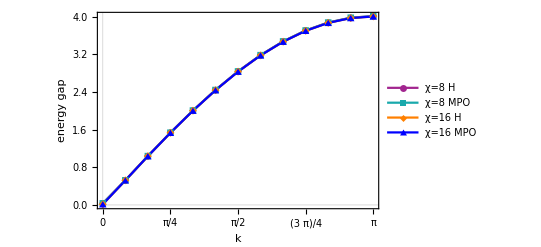

```mathematica
gap={{0.034022792873180926,0.5233769992999212,1.0379610052154,1.5350862712443503,2.0059126816509276,2.4424519254256736,2.8370662558980095,3.1831731045873526,3.4747910281056074,3.7069507410048073,3.875705781700252,3.978095406210058,4.012394495568416},{0.034022793067079116,0.5233769993260422,1.037961005295828,1.5350862712449884,2.0059126816284096,2.4424519254655186,2.8370662559308,3.1831731045300726,3.474791028051811,3.7069507409084785,3.875705781468054,3.9780954057498352,4.012394495101527},{0.014135334554457127,0.5225738586085501,1.0365103551668577,1.5326825725533066,2.0025759745624385,2.438224392466987,2.8321350528115534,3.1775901453026028,3.46867340512325,3.7003995945454173,3.868813418303316,3.971028471716269,4.0052935611326355},{0.014135329655954543,0.5225738618817211,1.0365103580745032,1.5326825745190384,2.002575974822417,2.4382243934789765,2.832135054488127,3.1775901470636856,3.4686734068596285,3.7003995952788986,3.868813418877597,3.971028473075072,4.005293562298034}};
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,Length[gap]},{i,1,Length[gap[[1]]]}];
Show[ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=8 H","χ=8 MPO","χ=16 H","χ=16 MPO"},{Scaled[{0.55,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k",None}},LabelStyle->{FontFamily->"Times",24,GrayLevel[0]},ImageSize->400]]
```

## 2D cylinder ground state

## Heisenberg 1/2

#### relative error-χ

different W converges with χ ~ W^3

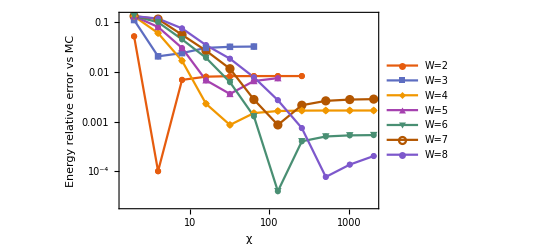

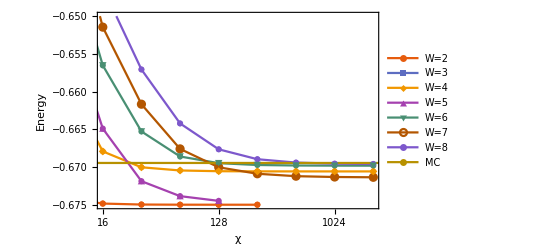

```mathematica
MC=-0.6694421;
VUMPS energy={{{2,-0.6345422353852718},{4,-0.6693750725665601},{8,-0.6740708028364285},{16,-0.6748180154569223},{32,-0.6749470895688596},{64,-0.6749678666920642},{128,-0.6749718756737937},{256,-0.6749726076182213}},
{{2,-0.5950420130004823},{4,-0.6556371161962462},{8,-0.6854858284988856},{16,-0.6898829051577726},{32,-0.6909250164316041},{64,-0.6911695878852653}},
{{2,-0.5807255723395672},{4,-0.6289009820451575},{8,-0.6581827324605429},{16,-0.6679116436055048},{32,-0.6700152111990748},{64,-0.6704352655820109},{128,-0.670534280154629},{256,-0.6705553485702883},{512,-0.6705600094668207},{1024,-0.6705609836997918},{2048,-0.6705611917227654}},
{{2,-0.5803957776084776},{4,-0.6155871157974815},{8,-0.6491312573617893},{16,-0.6648914580611334},{32,-0.6718543997744222},{64,-0.6738358713219867},{128,-0.674461448469279}},
{{2,-0.5802863569122595},{4,-0.6021683170351049},{8,-0.6391081626332298},{16,-0.6565218813985303},{32,-0.6652711591695919},{64,-0.6685860562665449},{128,-0.6694685551529367},{256,-0.6697103943816338},{512,-0.6697774868339195},{1024,-0.6697953451310992},{2048,-0.6697998458041077}},
{{2,-0.5802885254046235},{4,-0.5916919565314349},{8,-0.6319203875927313},{16,-0.6514578482481479},{32,-0.6616617568722862},{64,-0.6675806674660483},{128,-0.6700154545405153},{256,-0.6708704714692599},{512,-0.6711921065574642},{1024,-0.671300127405885},{2048,-0.6713388892639123}},
{{2,-0.5802856246676891},{4,-0.5898604035239774},{8,-0.618971358062268},{16,-0.6461842419580633},{32,-0.6570632874826308},{64,-0.6642083711260656},{128,-0.6676357939156123},{256,-0.6689463786573655},{512,-0.6693907529257728},{1024,-0.669533038556114},{2048,-0.6695775211138109}},{{1,MC},{10000,MC}}};
VUMPS energy aberror=Table[Table[{VUMPS energy[[j,i,1]],Abs[(MC-VUMPS energy[[j,i,2]])/MC]},{i,1,Length[VUMPS energy[[j]]]}],{j,1,Length[VUMPS energy]}];
ListLogLogPlot[VUMPS energy aberror,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotLegends->{"W=2","W=3","W=4","W=5","W=6","W=7","W=8"},Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,FrameTicks->{{Automatic,Automatic},{Table[2^i,{i,1,11}],Automatic}}, FrameLabel->{{"Energy relative error vs MC",None},{HoldForm["χ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
VUMPS energy=Table[Table[{Log[2,VUMPS energy[[j,i,1]]],VUMPS energy[[j,i,2]]},{i,1,Length[VUMPS energy[[j]]]}],{j,1,Length[VUMPS energy]}];
ListPlot[VUMPS energy,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotLegends->{"W=2","W=3","W=4","W=5","W=6","W=7","W=8","MC"},Joined->{True,True},Mesh->All,PlotRange->{{4,11},{-0.675,-0.65}},PlotTheme->"Scientific",PlotMarkers->Automatic,FrameTicks->{{Automatic,Automatic},{Table[{i,2^i},{i,1,11}],Automatic}},FrameLabel->{{"Energy",None},{HoldForm["χ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
```

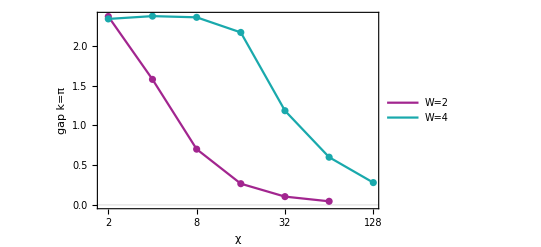

```mathematica
gap={{{2,2.3682995326094023},{4,1.5778290374666857},{8,0.700997413074341},{16,0.26693479526314223},{32,0.10454923858345622},{64,0.04569391867874051}},

{{2,2.337443145543327},{4,2.3726886317871876},{8,2.3576655682936165},{16,2.167870646240372},{32,1.1841260748149471},{64,0.5999046973750719},{128,0.2806654007072401}}};
gap=Table[Table[{Log[2,gap[[j,i,1]]],gap[[j,i,2]]},{i,1,Length[gap[[j]]]}],{j,1,Length[gap]}];
ListPlot[gap,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue,Black},PlotLegends->Placed[{"W=2","W=4","W=6","W=8"},{Scaled[{0.8,0.3}], {0, 0}}],Joined->{True,True},Mesh->All,PlotRange->All,PlotTheme->"Scientific",FrameTicks->{{Automatic,Automatic},{Table[{i,2^i},{i,1,10}],Automatic}},FrameLabel->{{"gap k=π",None},{HoldForm["χ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
```

## 2D TFIsing

#### relative error-χ

λ=3.04438

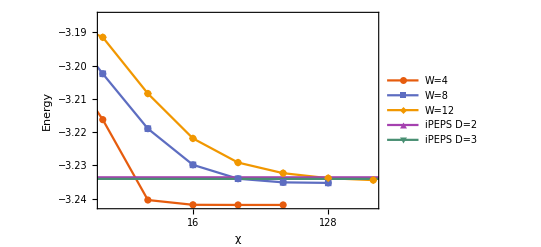

```mathematica
VUMPS energy={{{2.0,-3.1959809109946935},{4.0,-3.2162479192878943},{8.0,-3.240398658669554},{16.0,-3.2418346100489375},{32.0,-3.2418764483748355},{64.0,-3.241876828443563}},{{2.0,-3.1851321382291697},{4.0,-3.202456937924211},{8.0,-3.2189573331032997},{16.0,-3.229829395020305},{32.0,-3.234001630608466},{64.0,-3.235091226652238},{128,-3.2352536765040982}},{{2.0,-3.1851320275554977},{4.0,-3.191499490807927},{8.0,-3.2084072930547833},{16.0,-3.2218878351954476},{32.0,-3.2291435307962786},{64.0,-3.2323281174001},{128.0,-3.2338385834275236},{256,-3.2344125820594636}},{{1.0,-3.2335734175},{1024,-3.2335734175}},{{1.0,-3.234044774},{1024,-3.234044774}}};

VUMPS energy=Table[Table[{Log[2,VUMPS energy[[j,i,1]]],VUMPS energy[[j,i,2]]},{i,1,Length[VUMPS energy[[j]]]}],{j,1,Length[VUMPS energy]}];
ListPlot[VUMPS energy,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotLegends->{"W=4","W=8","W=12","iPEPS D=2","iPEPS D=3"},Joined->{True,True},Mesh->All,PlotRange->{{2,8},All},PlotTheme->"Scientific",PlotMarkers->Automatic,FrameTicks->{{Automatic,Automatic},{Table[{i,2^i},{i,1,11}],Automatic}},FrameLabel->{{"Energy",None},{HoldForm["χ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
```

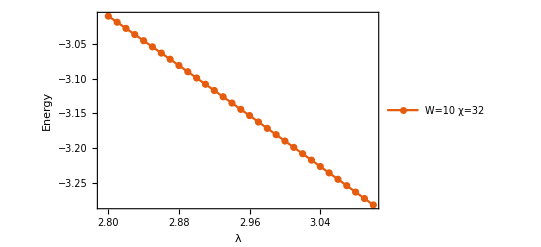

```mathematica
VUMPS energy={{2.8,-3.010678665478608},{2.81,-3.0194024753080573},{2.82,-3.0282205117999323},{2.83,-3.0370259658938936},{2.84,-3.0458522252974505},{2.85,-3.0546618501540097},{2.86,-3.0635644815055265},{2.87,-3.0723799446034334},{2.88,-3.0813521777528634},{2.89,-3.0902355282500187},{2.9,-3.099210607166064},{2.91,-3.108164979161845},{2.92,-3.117088834684581},{2.93,-3.1261214970908218},{2.94,-3.13508063112745},{2.95,-3.144138568585774},{2.96,-3.152991750593293},{2.97,-3.1622126897720197},{2.98,-3.171270127738998},{2.99,-3.180340642053185},{3.0,-3.1894238708525657},{3.01,-3.198519467055713},{3.02,-3.2076270976548193},{3.03,-3.2167112536870857},{3.04,-3.225877196477729},{3.05,-3.23501906323377},{3.06,-3.2441717602649724},{3.07,-3.253303152386475},{3.08,-3.262484152237047},{3.09,-3.2716757051287777},{3.1,-3.2808753004492512}};
ListPlot[VUMPS energy,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotLegends->{"W=10 χ=32"},Joined->{True,True},Mesh->All,PlotRange->All,PlotTheme->"Scientific",PlotMarkers->Automatic,FrameLabel->{{"Energy",None},{HoldForm["λ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
```

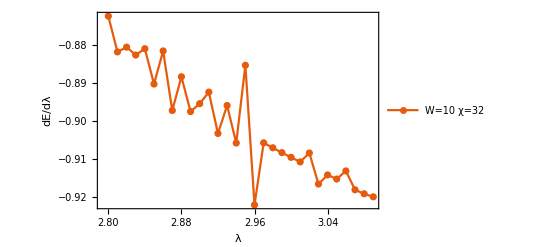

```mathematica
VUMPS energy={{2.8,-3.010678665478608},{2.81,-3.0194024753080573},{2.82,-3.0282205117999323},{2.83,-3.0370259658938936},{2.84,-3.0458522252974505},{2.85,-3.0546618501540097},{2.86,-3.0635644815055265},{2.87,-3.0723799446034334},{2.88,-3.0813521777528634},{2.89,-3.0902355282500187},{2.9,-3.099210607166064},{2.91,-3.108164979161845},{2.92,-3.117088834684581},{2.93,-3.1261214970908218},{2.94,-3.13508063112745},{2.95,-3.144138568585774},{2.96,-3.152991750593293},{2.97,-3.1622126897720197},{2.98,-3.171270127738998},{2.99,-3.180340642053185},{3.0,-3.1894238708525657},{3.01,-3.198519467055713},{3.02,-3.2076270976548193},{3.03,-3.2167112536870857},{3.04,-3.225877196477729},{3.05,-3.23501906323377},{3.06,-3.2441717602649724},{3.07,-3.253303152386475},{3.08,-3.262484152237047},{3.09,-3.2716757051287777},{3.1,-3.2808753004492512}};
VUMPS energy=Table[{VUMPS energy[[i]][[1]],(VUMPS energy[[i+1]][[2]]-VUMPS energy[[i]][[2]])/0.01},{i,1,Length[VUMPS energy]-1}];

ListPlot[VUMPS energy,PlotTheme->"Scientific",Mesh->All,Joined->True,PlotLegends->{"W=10 χ=32"},Joined->{True,True},Mesh->All,PlotRange->All,PlotTheme->"Scientific",PlotMarkers->Automatic,FrameLabel->{{"dE/dλ",None},{HoldForm["λ"],None}},LabelStyle->{FontFamily->"Times",14,GrayLevel[0]},ImageSize->400]
```

### energy gap λ=3.04438

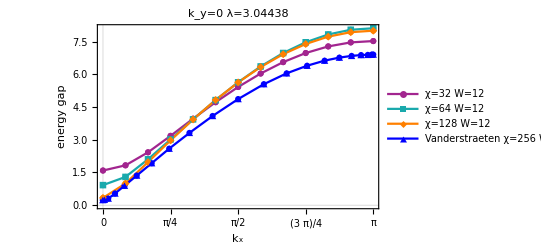

```mathematica
gap={{{0.,1.5899281069179683},{0.2617993877991494,1.8287940041001098},{0.5235987755982988,2.426270563881653},{0.7853981633974483,3.1810897847042745},{1.0471975511965976,3.9676141500852604},{1.3089969389957472,4.725996532407443},{1.5707963267948966,5.424394519270273},{1.8325957145940461,6.042377871699564},{2.0943951023931953,6.565402337940604},{2.356194490192345,6.982673613126656},{2.6179938779914944,7.286194159691364},{2.8797932657906435,7.470370160064337},{3.141592653589793,7.531878195180889}},{{0.,0.9206250412401955},{0.2617993877991494,1.2967534239952379},{0.5235987755982988,2.105368712020658},{0.7853981633974483,3.018091961903465},{1.0471975511965976,3.9373327817088515},{1.3089969389957472,4.821687085784255},{1.5707963267948966,5.639696936216481},{1.8325957145940461,6.366718351781176},{2.0943951023931953,6.9837616131260924},{2.356194490192345,7.476361371291919},{2.6179938779914944,7.834018717490424},{2.8797932657906435,8.049868516700005},{3.141592653589793,8.120285924517159}},{{0.,0.3331811468336374},{0.2617993877991494,0.994727746012301},{0.5235987755982988,1.977961206375543},{0.7853981633974483,2.97295179672538},{1.0471975511965976,3.933357818895178},{1.308996938995747,4.827663429932936},{1.5707963267948966,5.634843071406495},{1.832595714594046,6.339525523970805},{2.0943951023931953,6.929998108803353},{2.356194490192345,7.397388634999043},{2.617993877991494,7.735286105607969},{2.8797932657906435,7.939510093064581},{3.141592653589793,8.00781348074174}}};
Vanderstraeten 2022 2DTFIsing ky0=Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Vanderstraeten_2022_2DTFIsing_ky0_λ3.04438.csv"];
Show[ListPlot[{gap[[1]],gap[[2]],gap[[3]],Vanderstraeten 2022 2DTFIsing ky0},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=32 W=12","χ=64 W=12","χ=128 W=12","Vanderstraeten χ=256 W=12"},{Scaled[{0.4,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,PlotLabel->"k_y=0 λ=3.04438",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k_x",None}},LabelStyle->{FontFamily->"Times",15,GrayLevel[0]},ImageSize->400]]
```

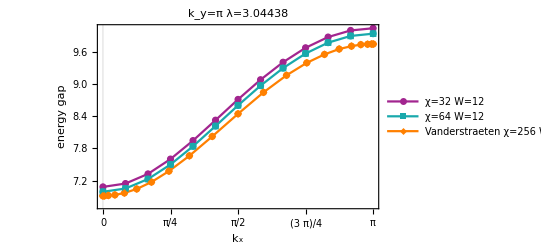

```mathematica
gap={{{0.0,7.081943737818446},{0.2617993877991494,7.144380625119563},{0.5235987755982988,7.324251559092945},{0.7853981633974483,7.600985806488207},{1.0471975511965976,7.945617054557962},{1.308996938995747,8.326438654615993},{1.5707963267948966,8.713418823784119},{1.832595714594046,9.080620038557461},{2.0943951023931953,9.407000228944787},{2.356194490192345,9.67629981896291},{2.617993877991494,9.876577575395391},{2.8797932657906435,9.999714359419684},{3.141592653589793,10.041022473524276}},
{{0.0,6.990768288644189},{0.2617993877991494,7.051771282101821},{0.5235987755982988,7.227857867698201},{0.7853981633974483,7.499658689613143},{1.0471975511965976,7.839558801237989},{1.308996938995747,8.216929407413012},{1.5707963267948966,8.602295830269233},{1.832595714594046,8.969729952283265},{2.0943951023931953,9.297775838951186},{2.356194490192345,9.56951842570051},{2.617993877991494,9.772295375599546},{2.8797932657906435,9.897346570115008},{3.141592653589793,9.939534536475183}}};
Vanderstraeten 2022 2DTFIsing kyπ=Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Vanderstraeten_2022_2DTFIsing_kyπ_λ3.04438.csv"];
Show[ListPlot[{gap[[1]],gap[[2]],Vanderstraeten 2022 2DTFIsing kyπ},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=32 W=12","χ=64 W=12","Vanderstraeten χ=256 W=12"},{Scaled[{0.4,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,PlotLabel->"k_y=π λ=3.04438",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k_x",None}},LabelStyle->{FontFamily->"Times",15,GrayLevel[0]},ImageSize->400]]
```

### energy gap λ=2.9

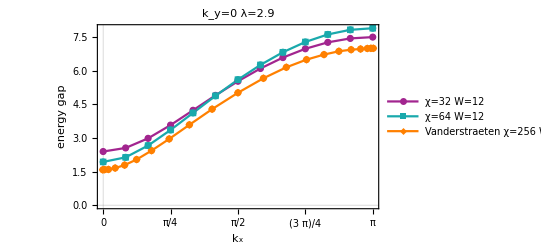

```mathematica
gap={{2.3906906870074716,2.550010986433576,2.9778293556269535,3.568672649612717,4.2280618427874295,4.892662838071383,5.522251205163866,6.08994978699242,6.5767051118934186,6.9685766920531265,7.255414335799473,7.4302331857072055,7.48893212818852},{1.9278405533025804,2.1313868448497244,2.656428591224037,3.3514942054759755,4.1102285518156645,4.870968115055211,5.593720413768729,6.249115059291281,6.814381258456061,7.271796229021017,7.608057024119546,7.813943073999122,7.88402291278284}};
Vanderstraeten 2022 2DTFIsing ky0=Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Vanderstraeten_2022_2DTFIsing_ky0_λ2.9.csv"];
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,Length[gap]},{i,1,Length[gap[[1]]]}];
Show[ListPlot[{gap[[1]],gap[[2]],Vanderstraeten 2022 2DTFIsing ky0},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=32 W=12","χ=64 W=12","Vanderstraeten χ=256 W=12"},{Scaled[{0.25,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,PlotLabel->"k_y=0 λ=2.9",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k_x",None}},LabelStyle->{FontFamily->"Times",15,GrayLevel[0]},ImageSize->400]]
```

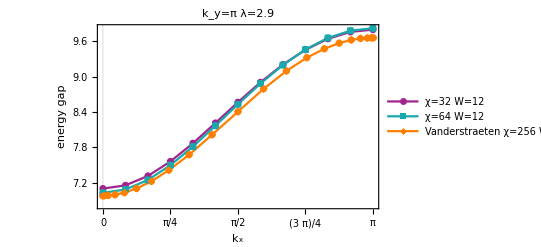

```mathematica
gap={{{0.0,7.102273401830272},{0.2617993877991494,7.157383443251158},{0.5235987755982988,7.316507155312621},{0.7853981633974483,7.562469751177843},{1.0471975511965976,7.870801569716172},{1.308996938995747,8.214156113289235},{1.5707963267948966,8.565932215768774},{1.832595714594046,8.902438236717106},{2.0943951023931953,9.203800003452464},{2.356194490192345,9.45412590523653},{2.617993877991494,9.641362107730735},{2.8797932657906435,9.75708082342599},{3.141592653589793,9.796299287247624}},
{{0.0,7.0309604691969865},{0.2617993877991494,7.086797876839424},{0.5235987755982988,7.248348831686106},{0.7853981633974483,7.498969981830395},{1.0471975511965976,7.814604211347929},{1.308996938995747,8.167899738115919},{1.5707963267948966,8.531742125778024},{1.832595714594046,8.881513702516065},{2.0943951023931953,9.196180845261754},{2.356194490192345,9.458628759123103},{2.617993877991494,9.655646036580292},{2.8797932657906435,9.77782345310101},{3.141592653589793,9.819490989113085}}};
Vanderstraeten 2022 2DTFIsing kyπ=Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Vanderstraeten_2022_2DTFIsing_kyπ_λ2.9.csv"];
Show[ListPlot[{gap[[1]],gap[[2]],Vanderstraeten 2022 2DTFIsing kyπ},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=32 W=12","χ=64 W=12","Vanderstraeten χ=256 W=12"},{Scaled[{0.4,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,PlotLabel->"k_y=π λ=2.9",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k_x",None}},LabelStyle->{FontFamily->"Times",15,GrayLevel[0]},ImageSize->400]]
```

### energy gap λ=2.5

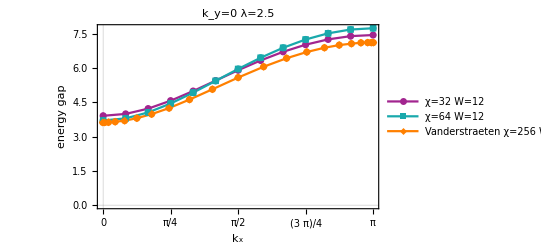

```mathematica
gap={{3.9119036946350763,3.993386472907642,4.224697770105718,4.572221369114186,4.994059120607778,5.44995262432904,5.905675860603859,6.333598138870848,6.711829327188031,7.023257834269521,7.254895926687837,7.39755114033359,7.445715347491431},{3.7063444575066598,3.7980594449265332,4.058176344233969,4.44893513583106,4.924357197846732,5.440708935739603,5.960288575354577,6.451589433119066,6.888582501397782,7.250187972566144,7.520074225210534,7.686623785803258,7.742906830959779}};
Vanderstraeten 2022 2DTFIsing ky0=Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Vanderstraeten_2022_2DTFIsing_ky0_λ2.5.csv"];
gap=Table[{Pi/12 (i-1),gap[[j]][[i]]},{j,1,Length[gap]},{i,1,Length[gap[[1]]]}];
Show[ListPlot[{gap[[1]],gap[[2]],Vanderstraeten 2022 2DTFIsing ky0},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=32 W=12","χ=64 W=12","Vanderstraeten χ=256 W=12"},{Scaled[{0.25,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,PlotLabel->"k_y=0 λ=2.5",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k_x",None}},LabelStyle->{FontFamily->"Times",15,GrayLevel[0]},ImageSize->400]]
```

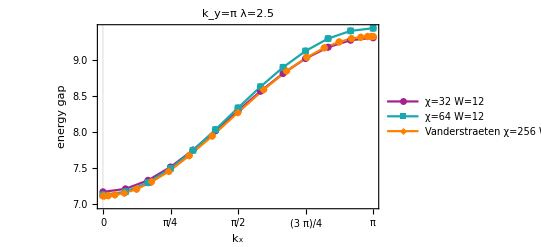

```mathematica
gap={{{0.0,7.167133046092452},{0.2617993877991494,7.207917258072566},{0.5235987755982988,7.326357352275176},{0.7853981633974483,7.511430089142179},{1.0471975511965976,7.746874403132141},{1.308996938995747,8.013560345516803},{1.5707963267948966,8.2916672243207},{1.832595714594046,8.562286567630702},{2.0943951023931953,8.808425203756894},{2.356194490192345,9.015586204215797},{2.617993877991494,9.172127875016496},{2.8797932657906435,9.26952562432605},{3.141592653589793,9.302575024179356}},
{{0.0,7.124852515824948},{0.2617993877991494,7.168150378330429},{0.5235987755982988,7.2940956119258304},{0.7853981633974483,7.491490786525985},{1.0471975511965976,7.743619451510625},{1.308996938995747,8.030506279066635},{1.5707963267948966,8.331088571934442},{1.832595714594046,8.62491168212617},{2.0943951023931953,8.893277635598935},{2.356194490192345,9.119979735389107},{2.617993877991494,9.291806598776612},{2.8797932657906435,9.39894827351347},{3.141592653589793,9.435346107260376}}};
Vanderstraeten 2022 2DTFIsing kyπ=Import["E:\\1 - research\\4.11 - Excitation_iPEPS\\AD_Excitation\\data\\Vanderstraeten_2022_2DTFIsing_kyπ_λ2.5.csv"];
Show[ListPlot[{gap[[1]],gap[[2]],Vanderstraeten 2022 2DTFIsing kyπ},PlotTheme->"Scientific",Mesh->All,Joined->True,PlotRange->All,PlotStyle->{colors [[1]],colors [[2]],colors [[3]],Blue},PlotLegends->Placed[{"χ=32 W=12","χ=64 W=12","Vanderstraeten χ=256 W=12"},{Scaled[{0.4,0.01}], {0, 0}}],Joined->{True,True},Mesh->All,PlotTheme->"Scientific",PlotMarkers->Automatic,PlotLabel->"k_y=π λ=2.5",FrameTicks->{{Automatic,Automatic},{{0,Pi/4,Pi/2,3Pi/4,Pi},Automatic}},FrameLabel->{{"energy gap",None},{"k_x",None}},LabelStyle->{FontFamily->"Times",15,GrayLevel[0]},ImageSize->400]]
```